# Trading strategies based on moving averages

## Inicialización

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"EconomicComputations.wl"}]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
```

### Loaded packages info

```mathematica
?AdvancedMapping`*
```

```mathematica
?EconomicComputations`*
```

## Load database

```mathematica
DatedPrices[dates_,prices_]:=Transpose[{dates,prices}];
```

```mathematica
path = FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Datasets","Prices","sp500v3.wdx"}];
database = Import[path];
```

## Strategy definition

Funciones para convertir fecha a fecha porcentual.

```mathematica
DaysInYear[year_] := First[DateDifference[{year, 1, 1}, {year, 12, 31}]] + 1;

YearPercentual[date_DateObject] := N[QuantityMagnitude[DateDifference[DateObject[{date["Year"], 1, 1}], date]] / DaysInYear[date["Year"]]] + date["Year"];
YearPercentual[date_String] := YearPercentual[DateObject[date]];

DateFromYearPercentual[yearPercentual_] := Block[{year, daysEllapsed, date},
	year = IntegerPart[yearPercentual];
	daysEllapsed = IntegerPart[(yearPercentual - year) * DaysInYear[year]];
	date = DatePlus[DateObject[{year, 1, 1}], daysEllapsed];
	Return[date];
];
```

Calcula intersecciones entre medias móviles.

```mathematica
RootsInRange[{f1_, f2_}, {t_, tmin_, tmax_}, opts___] := Module[
	{p, r, pts, x, f = Function[t, Evaluate[f1-f2]]},
	
	p = Plot[f[t], {t, tmin, tmax}];
	pts = Cases[First[p], Line[{x__}]->x, Infinity];
	r = Abs[Subtract@@Last@PlotRange[p]];
	pts = Map[First, Select[Split[pts, Sign[Last[#2]] == -Sign[Last[#1]] && Abs[Last[#2]-Last[#1]] < r/2&], Length[#1] == 2&], {2}];
	pts = (FindRoot[f[t]==0, {t, Sequence@@##}, Evaluate[Sequence@@FilterRules[{opts}, Options@FindRoot]]]&)/@pts;
	pts
];

RootsInRange[f1_==f2_, {t_, tmin_, tmax_}, opts___] := RootsInRange[{f1, f2}, {t, tmin, tmax}, opts];

Middle[l_List] := Part[l, Floor[Length[l]/2]];

VariableMovingAverage[l_List, f_] := Module[{subLists, windows}, 
	windows = Map[Ceiling[f[#]]&, l[[All, 2]]];
	subLists = DeleteCases[TakeList[l, Map[UpTo, windows]], {}];
	Map[{Middle[#[[All, 1]]], Mean[#[[All, 2]]]}&, subLists]
];

CrossoverTrading[datedPrices_, f1_, f2_] := Module[
	{
		avg1, avg2, datesMin, datesMax, priceInterpolation, avg1Interpolation, avg2Interpolation, 
		intersectionDates, x, firstInt, signals, buySignals, sellSignals, operations, return, result
	}, 

	avg1 = f1[datedPrices];
	avg2 = f2[datedPrices];
	datesMin = Max[{avg1[[1, 1]], avg2[[1, 1]]}];
	datesMax = Min[{avg1[[-1, 1]], avg2[[-1, 1]]}];

	priceInterpolation = Interpolation[datedPrices];
	avg1Interpolation = Interpolation[avg1];
	avg2Interpolation = Interpolation[avg2];
	
	intersectionDates = x /.RootsInRange[avg1Interpolation[x]==avg2Interpolation[x], {x, datesMin, datesMax}];
	
	(* Verificar que la primera intersección sea una operación de compra *)
	firstInt = First[intersectionDates];
	If[avg1Interpolation'[firstInt]-avg2Interpolation'[firstInt]<0, intersectionDates = Drop[intersectionDates, 1]];
	
	signals = Map[{#, priceInterpolation[#]}&, intersectionDates];
	buySignals = signals[[1;;-1;;2]];
	sellSignals = signals[[2;;-1;;2]];

	operations = Partition[priceInterpolation[intersectionDates], 2];
	return = Total[operations[[All, 2]]-operations[[All, 1]]];

	result = <|"BuySignals"->buySignals, "SellSignals"->sellSignals, "Return"->return|>;
	Return[result];
];
```

### Idea del algoritmo

Tomamos 100 muestras de precios.

```mathematica
market = First[database];
```

```mathematica
datos = Take[market["DatedPrices"],100]
```

{{2003-01-31,14.36},{2003-02-03,14.66},{2003-02-04,14.6},{2003-02-05,14.45},{2003-02-06,14.43},{2003-02-07,14.15},{2003-02-10,14.35},{2003-02-11,14.35},{2003-02-12,14.39},{2003-02-13,14.54},{2003-02-14,14.67},{2003-02-18,15.27},{2003-02-19,14.85},{2003-02-20,14.77},{2003-02-21,15.},{2003-02-24,14.74},{2003-02-25,15.02},{2003-02-26,14.5},{2003-02-27,14.86},{2003-02-28,15.01},{2003-03-03,14.65},{2003-03-04,14.56},{2003-03-05,14.62},{2003-03-06,14.56},{2003-03-07,14.53},{2003-03-10,14.37},{2003-03-11,14.23},{2003-03-12,14.22},{2003-03-13,14.72},{2003-03-14,14.78},{2003-03-17,15.01},{2003-03-18,15.},{2003-03-19,14.95},{2003-03-20,14.91},{2003-03-21,15.},{2003-03-24,14.37},{2003-03-25,14.55},{2003-03-26,14.41},{2003-03-27,14.49},{2003-03-28,14.57},{2003-03-31,14.14},{2003-04-01,14.16},{2003-04-02,14.6},{2003-04-03,14.46},{2003-04-04,14.41},{2003-04-07,14.49},{2003-04-08,14.45},{2003-04-09,14.19},{2003-04-10,14.37},{2003-04-11,13.2},{2003-04-14,13.58},{2003-04-15,13.39},{2003-04-16,13.24},{2003-04-17,13.12},{2003-04-21,13.14},{2003-04-22,13.51},{2003-04-23,13.58},{2003-04-24,13.44},{2003-04-25,13.35},{2003-04-28,13.86},{2003-04-29,14.06},{2003-04-30,14.22},{2003-05-01,14.36},{2003-05-02,14.45},{2003-05-05,16.09},{2003-05-06,17.5},{2003-05-07,17.65},{2003-05-08,18.},{2003-05-09,18.3},{2003-05-12,18.56},{2003-05-13,18.67},{2003-05-14,18.55},{2003-05-15,18.73},{2003-05-16,18.8},{2003-05-19,18.1},{2003-05-20,17.79},{2003-05-21,17.85},{2003-05-22,18.24},{2003-05-23,18.32},{2003-05-27,18.88},{2003-05-28,18.28},{2003-05-29,18.1},{2003-05-30,17.95},{2003-06-02,17.45},{2003-06-03,17.31},{2003-06-04,17.6},{2003-06-05,17.64},{2003-06-06,17.15},{2003-06-09,16.79},{2003-06-10,17.18},{2003-06-11,17.45},{2003-06-12,17.77},{2003-06-13,17.42},{2003-06-16,18.27},{2003-06-17,18.19},{2003-06-18,19.12},{2003-06-19,19.14},{2003-06-20,19.2},{2003-06-23,19.06},{2003-06-24,18.78}}

Para poder computar una media móvil es necesario pasar las fechas a fechas porcentuales.

```mathematica
datosPorcentuales = MapAt[YearPercentual, datos, {All,1}]
```

{{2003.08,14.36},{2003.09,14.66},{2003.09,14.6},{2003.1,14.45},{2003.1,14.43},{2003.1,14.15},{2003.11,14.35},{2003.11,14.35},{2003.12,14.39},{2003.12,14.54},{2003.12,14.67},{2003.13,15.27},{2003.13,14.85},{2003.14,14.77},{2003.14,15.},{2003.15,14.74},{2003.15,15.02},{2003.15,14.5},{2003.16,14.86},{2003.16,15.01},{2003.17,14.65},{2003.17,14.56},{2003.17,14.62},{2003.18,14.56},{2003.18,14.53},{2003.19,14.37},{2003.19,14.23},{2003.19,14.22},{2003.19,14.72},{2003.2,14.78},{2003.21,15.01},{2003.21,15.},{2003.21,14.95},{2003.21,14.91},{2003.22,15.},{2003.22,14.37},{2003.23,14.55},{2003.23,14.41},{2003.23,14.49},{2003.24,14.57},{2003.24,14.14},{2003.25,14.16},{2003.25,14.6},{2003.25,14.46},{2003.25,14.41},{2003.26,14.49},{2003.27,14.45},{2003.27,14.19},{2003.27,14.37},{2003.27,13.2},{2003.28,13.58},{2003.28,13.39},{2003.29,13.24},{2003.29,13.12},{2003.3,13.14},{2003.3,13.51},{2003.31,13.58},{2003.31,13.44},{2003.31,13.35},{2003.32,13.86},{2003.32,14.06},{2003.33,14.22},{2003.33,14.36},{2003.33,14.45},{2003.34,16.09},{2003.34,17.5},{2003.35,17.65},{2003.35,18.},{2003.35,18.3},{2003.36,18.56},{2003.36,18.67},{2003.36,18.55},{2003.37,18.73},{2003.37,18.8},{2003.38,18.1},{2003.38,17.79},{2003.38,17.85},{2003.39,18.24},{2003.39,18.32},{2003.4,18.88},{2003.4,18.28},{2003.41,18.1},{2003.41,17.95},{2003.42,17.45},{2003.42,17.31},{2003.42,17.6},{2003.42,17.64},{2003.43,17.15},{2003.44,16.79},{2003.44,17.18},{2003.44,17.45},{2003.44,17.77},{2003.45,17.42},{2003.45,18.27},{2003.46,18.19},{2003.46,19.12},{2003.46,19.14},{2003.47,19.2},{2003.47,19.06},{2003.48,18.78}}

Con esto se puede calcular la media móvil con diferentes ventanas

```mathematica
ma1 = MovingAverage[datosPorcentuales,10];
```

```mathematica
ma2 = MovingAverage[datosPorcentuales,20];
```

El usuario puede introducir la media móvil deseada al algoritmo. Aquí se utiliza la media móvil stándard en la primera función y una media móvil exponencial en la segunda función.

```mathematica
strategyResults = CrossoverTrading[
datosPorcentuales,
MovingAverage[#,10]&,
MovingAverage[#,20]&
]
```

<|BuySignals→{{2003.12,14.9827},{2003.2,14.864},{2003.24,14.1704},{2003.34,15.2556}},SellSignals→{{2003.16,14.8701},{2003.23,14.5569},{2003.27,14.1797},{2003.41,17.5706}},Return→1.90456|>

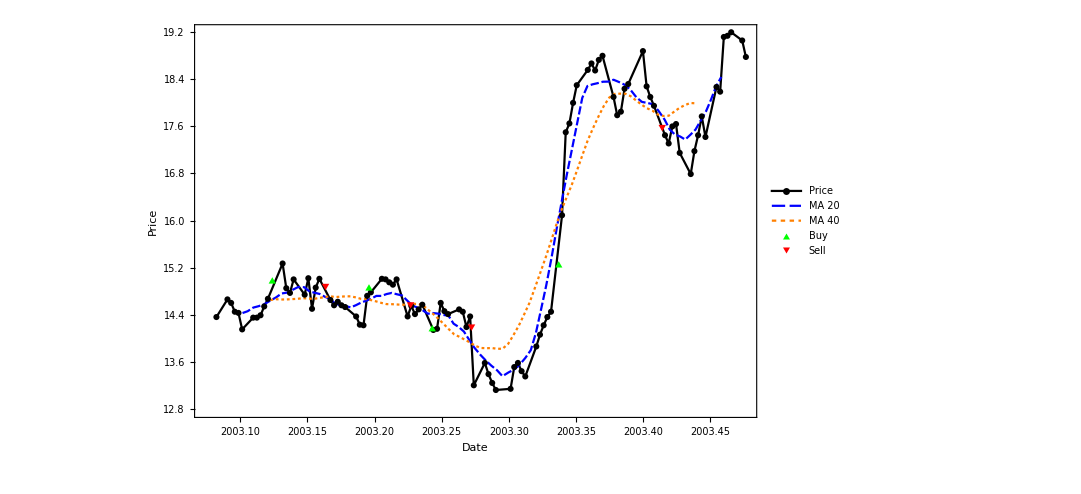

```mathematica
ListPlot[
{datosPorcentuales,ma1,ma2,strategyResults["BuySignals"],strategyResults["SellSignals"]},
Joined->{True,True,True,False,False},
PlotTheme->"Monochrome",
FrameLabel->{Style["Date",bigFontSize],Style["Price",bigFontSize]},
PlotLegends->{"Price","MA 20","MA 40","Buy","Sell"},
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->{Black,{Thick,Blue},{Thick,Orange},Green,Red},
PlotMarkers->{Automatic,None,None,Automatic,Automatic},
ImageSize->800
]
```

```mathematica
CrossoverSMAReturns[marketIndex_,maWindow1_,maWindow2_]:=CrossoverTrading[
database[[marketIndex]]["DatedPrices"],
MovingAverage[#,maWindow1]&,
MovingAverage[#,maWindow2]&
]["Return"];
TradeInMarket[maWindow1_,maWindow2_]:=Module[{i},ProgressParallelTable[CrossoverSMAReturns[i,maWindow1,maWindow2],{i,1,Length[database]}]];
SampleCrossoverSMAReturns[datedPrices_,maWindow1_,maWindow2_]:=CrossoverTrading[
datedPrices,
MovingAverage[#,maWindow1]&,
MovingAverage[#,maWindow2]&
]["Return"];
TradeOnSample[sample_,maWindow1_,maWindow2_]:=Module[{i},
Table[SampleCrossoverSMAReturns[sample[[i]],maWindow1,maWindow2],{i,1,Length[sample]}]
];
ProbabilityOfPositive[data_]:=Module[{x},Probability[x>0,x\[Distributed]EmpiricalDistribution[data]]];
```

### Prueba de estrategia SMA en componentes del S&P 500.

```mathematica
SaveKernelState[path_:FileNameJoin[{NotebookDirectory[],StringJoin[FileBaseName[NotebookFileName[]],"_state.mx"]}]]:=DumpSave[path,"Global`"];
LoadKernelState[path_:FileNameJoin[{NotebookDirectory[],StringJoin[FileBaseName[NotebookFileName[]],"_state.mx"]}]]:=Get[path];
```

```mathematica
tradingResults = Table[{w1,w2,TradeInMarket[w1,w2]},{w1,10,200,10},{w2,w1+10,200,10}];
```

```mathematica
SaveKernelState[]
```

{Global`}

Probabilidad de retorno positivo

```mathematica
probabilityOfEarning = Map[MapAt[ProbabilityOfPositive,#,{All,3}]&,DeleteCases[tradingResults,{}]];
```

```mathematica
sparseArray = Flatten[Map[{#[[1]],#[[2]]}/10->#[[3]]&,probabilityOfEarning,{2}],1];
```

```mathematica
array = SparseArray[Select[sparseArray,Last[#]>0.5&]];
```

```mathematica
MatrixPlot[array,
ColorFunction->"Rainbow",
PlotLegends->Automatic,
PlotLabel->Style["Probabilidad de retorno positivo",bigFontSize,Black],
PlotTheme->"Monochrome",
FrameLabel->{Style["W1 (%10)",bigFontSize],Style["W2 (%10)",bigFontSize]}
]
```

-Graphics-

Media

```mathematica
returnMean = Map[MapAt[Mean,#,{All,3}]&,DeleteCases[tradingResults,{}]];
```

```mathematica
meanSparseArray = Flatten[Map[{#[[1]],#[[2]]}/10->#[[3]]&,returnMean,{2}],1];
```

```mathematica
meanArray = SparseArray[meanSparseArray];
```

```mathematica
MatrixPlot[meanArray,
ColorFunction->"Rainbow",
PlotLegends->Automatic,
PlotLabel->Style["Media de los retornos",bigFontSize,Black],
PlotTheme->"Monochrome",
FrameLabel->{Style["W1 (%10)",bigFontSize],Style["W2 (%10)",bigFontSize]}
]
```

-Graphics-

### Cómputo de ventana óptima

```mathematica
sample = Take[database[[All,"DatedPrices"]],All,1000];
```

```mathematica
fixDates =  ProgressParallelMap[MapAt[YearPercentual, #, {All,1}]&,sample,Method->"CoarsestGrained"];
```

```mathematica
windows = Flatten[Table[{w1,w2},{w1,10,200,10},{w2,w1+10,200,10}],1];
```

```mathematica
tradingResults = ProgressParallelMap[{First[#],Last[#],TradeOnSample[fixDates,First[#],Last[#]]}&,windows,Method->"CoarsestGrained"];
```

```mathematica
probabilityOfEarning = MapAt[ProbabilityOfPositive,DeleteCases[tradingResults,{}],{All,3}];
sparseArray = Flatten[Map[{#[[1]],#[[2]]}/10->#[[3]]&,probabilityOfEarning],1];
array = SparseArray[Select[sparseArray,Last[#]>0.5&]];
MatrixPlot[array,
ColorFunction->"Rainbow",
PlotLegends->Automatic,
PlotLabel->Style["Probabilidad de retorno positivo",bigFontSize,Black],
PlotTheme->"Monochrome",
FrameLabel->{Style["W1 (%10)",bigFontSize],Style["W2 (%10)",bigFontSize]}
]
```

-Graphics-